```mathematica
ClearAll["Global`*"]
```

```mathematica
Series[(vv/c+x)/(1/c+(vv x)/c^2),{x,0,2}]
```

vv+(c-vv^2/c) x+(-vv+vv^3/c^2) x^2+O[x]^3

```mathematica
Series[(vv+w)/(1+(vv w)/c^2),{w,0,3}]
```

vv+(1-vv^2/c^2) w+(-vv/c^2+vv^3/c^4) w^2+(vv^2/c^4-vv^4/c^6) w^3+O[w]^4

```mathematica
Series[(c/n+w)/(1+(c/n w)/c^2),{w,0,3}]
```

c/n+(1-1/n^2) w+((1-n^2) w^2)/(c n^3)+((-1+n^2) w^3)/(c^2 n^4)+O[w]^4

```mathematica
Plot[Cos[9*2π x]+Cos[10*2π x],{x,0,5}]
```

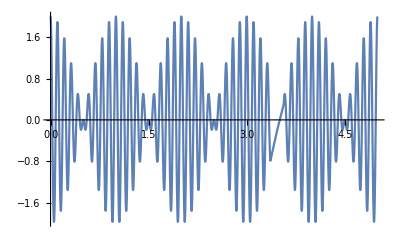

```mathematica
Cos[a x]+Cos[b x]//TrigFactor
```

2 Cos[(a x)/2-(b x)/2] Cos[(a x)/2+(b x)/2]